```mathematica
ClearAll["Global`*"]
```

```mathematica
tk[n_,k_, a_]:= tk[n,k,a]=Sum[ tk[n/j,k-1,a],{j,2,n}]-a Sum[ tk[n/(a j),k-1,a],{j,1,n/a}];tk[n_,0,a_]:=1

tk1b[n_,k_,a_]:=Sum[t[j,a]tk1b[n/j,k-1,a],{j,1,n}];tk1b[n_,0,a_]:=1

tk1[n_,k_, a_]:= tk1[n,k,a]=Sum[ tk1[n/j,k-1,a],{j,1,n}]-a Sum[ tk1[n/(a j),k-1,a],{j,1,n/a}];tk1[n_,0,a_]:=1


tki[n_,k_,k2_,a_]:=tki[n,k,k2,a]=Sum[ tki[n/j,k-1,k2,a],{j,2,n}]
tki[n_,0,k2_,a_]:=tkp[n,k2,a]
tkp[n_,k_,a_]:=tkp[n,k,a]=Sum[ tkp[n/(a j),k-1,a],{j,1,n/a}]
tkp[n_,0,a_]:=1
tk2[n_,k_,a_]:=tk2[n,k,a]=Sum[ (-1)^j a^j Binomial[k,j]tki[n,k-j,j,a],{j,0,k}]
tk2s[n_,k_,j_,a_]:=(-1)^j a^j Binomial[k,j]tki[n,k-j,j,a]
tk2s2[n_,k_,j_,a_]:=tki[n,k-j,j,a]

tk2a[n_,k_,a_]:=tk2a[n,k,a]=Sum[(-1)^j Binomial[k,j]tk1[n,k-j,a],{j,0,k}]

tk1z[n_,z_,b_]:=Sum[FactorialPower[z,j]/j! tk2[n,j,b],{j,0,Log[If[b≤2,b,2],n]}]

D1[n_,k_]:=Sum[D1[Floor[n/j],k-1],{j,1,n}];D1[n_,0]:=1
Lina[n_,a_]:=Sum[ ((-1)^(k+1) tk2[n,k,a]+1)/k + (a^k-1)/k,{k,1,Log[a,n]}]
Linb[n_,a_]:=Sum[ (-1)^(k+1)/k tk[n,k,a],{k,1,Log[2,n]}]+Sum[ a^k/k,{k,1,Log[a,n]}]
Lin2[n_,a_]:=If[a>=2,Linb[n,a],Lina[n,a]]

d[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}

d2[n_,k_]:=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1

DD[n_,z_]:=Sum[d[j,z],{j,1,n}]

st[n_,a_,k_]:=If[tk2[a,n,k]≠0,(-1)^(n+1)/n tk2[a,n,k] + 1/n,0]
```

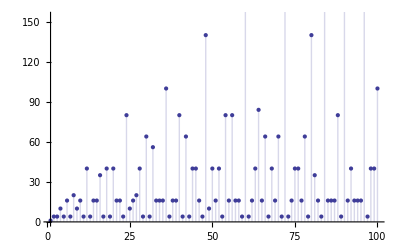

```mathematica
DiscretePlot[ {tk1[n,4,1.0000001]},{n,1,100}]
```

```mathematica
Table[{n,d[n,4],tk1[n,4,1.0000001]},{n,1,100}]//TableForm
```

1 | 1 | 1.
2 | 4 | 4.
3 | 4 | 4.
4 | 10 | 10.
5 | 4 | 4.
6 | 16 | 16.
7 | 4 | 4.
8 | 20 | 20.
9 | 10 | 10.
10 | 16 | 16.
11 | 4 | 4.
12 | 40 | 40.
13 | 4 | 4.
14 | 16 | 16.
15 | 16 | 16.
16 | 35 | 35.
17 | 4 | 4.
18 | 40 | 40.
19 | 4 | 4.
20 | 40 | 40.
21 | 16 | 16.
22 | 16 | 16.
23 | 4 | 4.
24 | 80 | 80.
25 | 10 | 10.
26 | 16 | 16.
27 | 20 | 20.
28 | 40 | 40.
29 | 4 | 4.
30 | 64 | 64.
31 | 4 | 4.
32 | 56 | 56.
33 | 16 | 16.
34 | 16 | 16.
35 | 16 | 16.
36 | 100 | 100.
37 | 4 | 4.
38 | 16 | 16.
39 | 16 | 16.
40 | 80 | 80.
41 | 4 | 4.
42 | 64 | 64.
43 | 4 | 4.
44 | 40 | 40.
45 | 40 | 40.
46 | 16 | 16.
47 | 4 | 4.
48 | 140 | 140.
49 | 10 | 10.
50 | 40 | 40.
51 | 16 | 16.
52 | 40 | 40.
53 | 4 | 4.
54 | 80 | 80.
55 | 16 | 16.
56 | 80 | 80.
57 | 16 | 16.
58 | 16 | 16.
59 | 4 | 4.
60 | 160 | 160.
61 | 4 | 4.
62 | 16 | 16.
63 | 40 | 40.
64 | 84 | 84.
65 | 16 | 16.
66 | 64 | 64.
67 | 4 | 4.
68 | 40 | 40.
69 | 16 | 16.
70 | 64 | 64.
71 | 4 | 4.
72 | 200 | 200.
73 | 4 | 4.
74 | 16 | 16.
75 | 40 | 40.
76 | 40 | 40.
77 | 16 | 16.
78 | 64 | 64.
79 | 4 | 4.
80 | 140 | 140.
81 | 35 | 35.
82 | 16 | 16.
83 | 4 | 4.
84 | 160 | 160.
85 | 16 | 16.
86 | 16 | 16.
87 | 16 | 16.
88 | 80 | 80.
89 | 4 | 4.
90 | 160 | 160.
91 | 16 | 16.
92 | 40 | 40.
93 | 16 | 16.
94 | 16 | 16.
95 | 16 | 16.
96 | 224 | 224.
97 | 4 | 4.
98 | 40 | 40.
99 | 40 | 40.
100 | 100 | 100.

```mathematica
Table[{n,d2[n,4]+1,tk[n,4,1.0000001]},{n,1,100}]//TableForm
```

1 | 1 | 0.
2 | 1 | 1.
3 | 1 | 1.
4 | 1 | 1.
5 | 1 | 1.
6 | 1 | 1.
7 | 1 | 1.
8 | 1 | 1.
9 | 1 | 1.
10 | 1 | 1.
11 | 1 | 1.
12 | 1 | 1.
13 | 1 | 1.
14 | 1 | 1.00001
15 | 1 | 1.00001
16 | 2 | 2.00001
17 | 1 | 1.00001
18 | 1 | 1.00001
19 | 1 | 1.00001
20 | 1 | 1.00001
21 | 1 | 1.00001
22 | 1 | 1.00001
23 | 1 | 1.00001
24 | 5 | 5.00001
25 | 1 | 1.00001
26 | 1 | 1.00001
27 | 1 | 1.00001
28 | 1 | 1.00001
29 | 1 | 1.00001
30 | 1 | 1.00001
31 | 1 | 1.00001
32 | 5 | 5.00001
33 | 1 | 1.00001
34 | 1 | 1.00001
35 | 1 | 1.00001
36 | 7 | 7.00001
37 | 1 | 1.00001
38 | 1 | 1.00001
39 | 1 | 1.00002
40 | 5 | 5.00002
41 | 1 | 1.00002
42 | 1 | 1.00002
43 | 1 | 1.00002
44 | 1 | 1.00002
45 | 1 | 1.00002
46 | 1 | 1.00002
47 | 1 | 1.00002
48 | 17 | 17.
49 | 1 | 1.00002
50 | 1 | 1.00002
51 | 1 | 1.00002
52 | 1 | 1.00002
53 | 1 | 1.00002
54 | 5 | 5.00002
55 | 1 | 1.00002
56 | 5 | 5.00002
57 | 1 | 1.00002
58 | 1 | 1.00002
59 | 1 | 1.00002
60 | 13 | 13.
61 | 1 | 1.00002
62 | 1 | 1.00002
63 | 1 | 1.00002
64 | 11 | 11.
65 | 1 | 1.00003
66 | 1 | 1.00003
67 | 1 | 1.00003
68 | 1 | 1.00003
69 | 1 | 1.00003
70 | 1 | 1.00003
71 | 1 | 1.00003
72 | 29 | 29.
73 | 1 | 1.00003
74 | 1 | 1.00003
75 | 1 | 1.00003
76 | 1 | 1.00003
77 | 1 | 1.00003
78 | 1 | 1.00003
79 | 1 | 1.00003
80 | 17 | 17.
81 | 2 | 2.00003
82 | 1 | 1.00003
83 | 1 | 1.00003
84 | 13 | 13.
85 | 1 | 1.00003
86 | 1 | 1.00003
87 | 1 | 1.00003
88 | 5 | 5.00003
89 | 1 | 1.00004
90 | 13 | 13.
91 | 1 | 1.00004
92 | 1 | 1.00004
93 | 1 | 1.00004
94 | 1 | 1.00004
95 | 1 | 1.00004
96 | 41 | 41.
97 | 1 | 1.00004
98 | 1 | 1.00004
99 | 1 | 1.00004
100 | 7 | 7.00004

```mathematica
Table[{n,d2[n,3]-1,tk[n,3,1.0000001]},{n,1,100}]//TableForm
```

1 | -1 | 0.
2 | -1 | -1.
3 | -1 | -1.
4 | -1 | -1.
5 | -1 | -1.
6 | -1 | -1.
7 | -1 | -1.
8 | 0 | -2.1×10^-6
9 | -1 | -1.
10 | -1 | -1.
11 | -1 | -1.
12 | 2 | 2.
13 | -1 | -1.
14 | -1 | -1.
15 | -1 | -1.
16 | 2 | 2.
17 | -1 | -1.
18 | 2 | 1.99999
19 | -1 | -1.00001
20 | 2 | 1.99999
21 | -1 | -1.00001
22 | -1 | -1.00001
23 | -1 | -1.00001
24 | 8 | 7.99999
25 | -1 | -1.00001
26 | -1 | -1.00001
27 | 0 | -7.8×10^-6
28 | 2 | 1.99999
29 | -1 | -1.00001
30 | 5 | 4.99999
31 | -1 | -1.00001
32 | 5 | 4.99999
33 | -1 | -1.00001
34 | -1 | -1.00001
35 | -1 | -1.00001
36 | 11 | 11.
37 | -1 | -1.00001
38 | -1 | -1.00001
39 | -1 | -1.00001
40 | 8 | 7.99999
41 | -1 | -1.00001
42 | 5 | 4.99999
43 | -1 | -1.00001
44 | 2 | 1.99999
45 | 2 | 1.99999
46 | -1 | -1.00001
47 | -1 | -1.00001
48 | 17 | 17.
49 | -1 | -1.00001
50 | 2 | 1.99999
51 | -1 | -1.00002
52 | 2 | 1.99998
53 | -1 | -1.00002
54 | 8 | 7.99998
55 | -1 | -1.00002
56 | 8 | 7.99998
57 | -1 | -1.00002
58 | -1 | -1.00002
59 | -1 | -1.00002
60 | 20 | 20.
61 | -1 | -1.00002
62 | -1 | -1.00002
63 | 2 | 1.99998
64 | 9 | 8.99998
65 | -1 | -1.00002
66 | 5 | 4.99998
67 | -1 | -1.00002
68 | 2 | 1.99998
69 | -1 | -1.00002
70 | 5 | 4.99998
71 | -1 | -1.00002
72 | 26 | 26.
73 | -1 | -1.00002
74 | -1 | -1.00002
75 | 2 | 1.99998
76 | 2 | 1.99998
77 | -1 | -1.00002
78 | 5 | 4.99998
79 | -1 | -1.00002
80 | 17 | 17.
81 | 2 | 1.99998
82 | -1 | -1.00002
83 | -1 | -1.00002
84 | 20 | 20.
85 | -1 | -1.00003
86 | -1 | -1.00003
87 | -1 | -1.00003
88 | 8 | 7.99997
89 | -1 | -1.00003
90 | 20 | 20.
91 | -1 | -1.00003
92 | 2 | 1.99997
93 | -1 | -1.00003
94 | -1 | -1.00003
95 | -1 | -1.00003
96 | 29 | 29.
97 | -1 | -1.00003
98 | 2 | 1.99997
99 | 2 | 1.99997
100 | 11 | 11.

```mathematica
Table[{n,d2[n,8]+1,tk[n,8,1.0000001]},{n,1,100}]//TableForm
```

1 | 1 | 0.
2 | 1 | 1.
3 | 1 | 1.
4 | 1 | 1.
5 | 1 | 1.
6 | 1 | 1.
7 | 1 | 1.
8 | 1 | 1.00001
9 | 1 | 1.00001
10 | 1 | 1.00001
11 | 1 | 1.00001
12 | 1 | 1.00001
13 | 1 | 1.00001
14 | 1 | 1.00001
15 | 1 | 1.00001
16 | 1 | 1.00001
17 | 1 | 1.00001
18 | 1 | 1.00001
19 | 1 | 1.00001
20 | 1 | 1.00002
21 | 1 | 1.00002
22 | 1 | 1.00002
23 | 1 | 1.00002
24 | 1 | 1.00002
25 | 1 | 1.00002
26 | 1 | 1.00002
27 | 1 | 1.00002
28 | 1 | 1.00002
29 | 1 | 1.00002
30 | 1 | 1.00002
31 | 1 | 1.00002
32 | 1 | 1.00002
33 | 1 | 1.00003
34 | 1 | 1.00003
35 | 1 | 1.00003
36 | 1 | 1.00003
37 | 1 | 1.00003
38 | 1 | 1.00003
39 | 1 | 1.00003
40 | 1 | 1.00003
41 | 1 | 1.00003
42 | 1 | 1.00003
43 | 1 | 1.00003
44 | 1 | 1.00003
45 | 1 | 1.00004
46 | 1 | 1.00004
47 | 1 | 1.00004
48 | 1 | 1.00004
49 | 1 | 1.00004
50 | 1 | 1.00004
51 | 1 | 1.00004
52 | 1 | 1.00004
53 | 1 | 1.00004
54 | 1 | 1.00004
55 | 1 | 1.00004
56 | 1 | 1.00004
57 | 1 | 1.00004
58 | 1 | 1.00005
59 | 1 | 1.00005
60 | 1 | 1.00005
61 | 1 | 1.00005
62 | 1 | 1.00005
63 | 1 | 1.00005
64 | 1 | 1.00005
65 | 1 | 1.00005
66 | 1 | 1.00005
67 | 1 | 1.00005
68 | 1 | 1.00005
69 | 1 | 1.00005
70 | 1 | 1.00006
71 | 1 | 1.00006
72 | 1 | 1.00006
73 | 1 | 1.00006
74 | 1 | 1.00006
75 | 1 | 1.00006
76 | 1 | 1.00006
77 | 1 | 1.00006
78 | 1 | 1.00006
79 | 1 | 1.00006
80 | 1 | 1.00006
81 | 1 | 1.00006
82 | 1 | 1.00006
83 | 1 | 1.00007
84 | 1 | 1.00007
85 | 1 | 1.00007
86 | 1 | 1.00007
87 | 1 | 1.00007
88 | 1 | 1.00007
89 | 1 | 1.00007
90 | 1 | 1.00007
91 | 1 | 1.00007
92 | 1 | 1.00007
93 | 1 | 1.00007
94 | 1 | 1.00007
95 | 1 | 1.00008
96 | 1 | 1.00008
97 | 1 | 1.00008
98 | 1 | 1.00008
99 | 1 | 1.00008
100 | 1 | 1.00008

```mathematica
Table[ {n, aa=(tk1[n,1,1.1]-tk1[n-1,1,1.1]),bb=(Mod[n+.0001,1.1]-Mod[n+.0001-1,1.1]),aa-bb},{n,2,120}]//TableForm
```

2 | -0.1 | -0.1 | 0.
3 | -0.1 | -0.1 | 0.
4 | -0.1 | -0.1 | 0.
5 | -0.1 | -0.1 | 0.
6 | -0.1 | -0.1 | 4.44089×10^-16
7 | -0.1 | -0.1 | -4.44089×10^-16
8 | -0.1 | -0.1 | -4.44089×10^-16
9 | -0.1 | -0.1 | 4.44089×10^-16
10 | -0.1 | -0.1 | 4.44089×10^-16
11 | -0.1 | -0.1 | 4.44089×10^-16
12 | 1. | 1. | 0.
13 | -0.1 | -0.1 | -1.33227×10^-15
14 | -0.1 | -0.1 | 4.44089×10^-16
15 | -0.1 | -0.1 | 4.44089×10^-16
16 | -0.1 | -0.1 | -1.33227×10^-15
17 | -0.1 | -0.1 | 2.22045×10^-15
18 | -0.1 | -0.1 | -1.33227×10^-15
19 | -0.1 | -0.1 | -1.33227×10^-15
20 | -0.1 | -0.1 | 2.22045×10^-15
21 | -0.1 | -0.1 | -1.33227×10^-15
22 | -0.1 | -0.1 | 2.22045×10^-15
23 | 1. | 1. | 0.
24 | -0.1 | -0.1 | -1.33227×10^-15
25 | -0.1 | -0.1 | -1.33227×10^-15
26 | -0.1 | -0.1 | 2.22045×10^-15
27 | -0.1 | -0.1 | -1.33227×10^-15
28 | -0.1 | -0.1 | -1.33227×10^-15
29 | -0.1 | -0.1 | 2.22045×10^-15
30 | -0.1 | -0.1 | -1.33227×10^-15
31 | -0.1 | -0.1 | -1.33227×10^-15
32 | -0.1 | -0.1 | 2.22045×10^-15
33 | -0.1 | -0.1 | 2.22045×10^-15
34 | 1. | 1. | 0.
35 | -0.1 | -0.1 | -1.33227×10^-15
36 | -0.1 | -0.1 | -1.33227×10^-15
37 | -0.1 | -0.1 | -1.33227×10^-15
38 | -0.1 | -0.1 | -1.33227×10^-15
39 | -0.1 | -0.1 | 5.77316×10^-15
40 | -0.1 | -0.1 | -1.33227×10^-15
41 | -0.1 | -0.1 | -1.33227×10^-15
42 | -0.1 | -0.1 | -1.33227×10^-15
43 | -0.1 | -0.1 | -1.33227×10^-15
44 | -0.1 | -0.1 | 5.77316×10^-15
45 | 1. | 1. | 0.
46 | -0.1 | -0.1 | -1.33227×10^-15
47 | -0.1 | -0.1 | -1.33227×10^-15
48 | -0.1 | -0.1 | -1.33227×10^-15
49 | -0.1 | -0.1 | -1.33227×10^-15
50 | -0.1 | -0.1 | -1.33227×10^-15
51 | -0.1 | -0.1 | 5.77316×10^-15
52 | -0.1 | -0.1 | -1.33227×10^-15
53 | -0.1 | -0.1 | -1.33227×10^-15
54 | -0.1 | -0.1 | -1.33227×10^-15
55 | -0.1 | -0.1 | -1.33227×10^-15
56 | 1. | 1. | 0.
57 | -0.1 | -0.1 | 5.77316×10^-15
58 | -0.1 | -0.1 | -1.33227×10^-15
59 | -0.1 | -0.1 | -1.33227×10^-15
60 | -0.1 | -0.1 | -1.33227×10^-15
61 | -0.1 | -0.1 | -1.33227×10^-15
62 | -0.1 | -0.1 | -1.33227×10^-15
63 | -0.1 | -0.1 | 5.77316×10^-15
64 | -0.1 | -0.1 | -1.33227×10^-15
65 | -0.1 | -0.1 | -1.33227×10^-15
66 | -0.1 | -0.1 | 5.77316×10^-15
67 | 1. | 1. | 0.
68 | -0.1 | -0.1 | -8.43769×10^-15
69 | -0.1 | -0.1 | 5.77316×10^-15
70 | -0.1 | -0.1 | -8.43769×10^-15
71 | -0.1 | -0.1 | 5.77316×10^-15
72 | -0.1 | -0.1 | 5.77316×10^-15
73 | -0.1 | -0.1 | -8.43769×10^-15
74 | -0.1 | -0.1 | 5.77316×10^-15
75 | -0.1 | -0.1 | -8.43769×10^-15
76 | -0.1 | -0.1 | 5.77316×10^-15
77 | -0.1 | -0.1 | 5.77316×10^-15
78 | 1. | 1. | 0.
79 | -0.1 | -0.1 | -8.43769×10^-15
80 | -0.1 | -0.1 | 5.77316×10^-15
81 | -0.1 | -0.1 | -8.43769×10^-15
82 | -0.1 | -0.1 | 5.77316×10^-15
83 | -0.1 | -0.1 | 5.77316×10^-15
84 | -0.1 | -0.1 | -8.43769×10^-15
85 | -0.1 | -0.1 | 5.77316×10^-15
86 | -0.1 | -0.1 | -8.43769×10^-15
87 | -0.1 | -0.1 | 5.77316×10^-15
88 | -0.1 | -0.1 | 5.77316×10^-15
89 | 1. | 1. | 0.
90 | -0.1 | -0.1 | -8.43769×10^-15
91 | -0.1 | -0.1 | 5.77316×10^-15
92 | -0.1 | -0.1 | -8.43769×10^-15
93 | -0.1 | -0.1 | 5.77316×10^-15
94 | -0.1 | -0.1 | -8.43769×10^-15
95 | -0.1 | -0.1 | 5.77316×10^-15
96 | -0.1 | -0.1 | 5.77316×10^-15
97 | -0.1 | -0.1 | -8.43769×10^-15
98 | -0.1 | -0.1 | 5.77316×10^-15
99 | -0.1 | -0.1 | -8.43769×10^-15
100 | 1. | 1. | 0.
101 | -0.1 | -0.1 | 5.77316×10^-15
102 | -0.1 | -0.1 | 5.77316×10^-15
103 | -0.1 | -0.1 | -8.43769×10^-15
104 | -0.1 | -0.1 | 5.77316×10^-15
105 | -0.1 | -0.1 | -8.43769×10^-15
106 | -0.1 | -0.1 | 5.77316×10^-15
107 | -0.1 | -0.1 | 5.77316×10^-15
108 | -0.1 | -0.1 | -8.43769×10^-15
109 | -0.1 | -0.1 | 5.77316×10^-15
110 | -0.1 | -0.1 | -8.43769×10^-15
111 | 1. | 1. | 0.
112 | -0.1 | -0.1 | 5.77316×10^-15
113 | -0.1 | -0.1 | 5.77316×10^-15
114 | -0.1 | -0.1 | -8.43769×10^-15
115 | -0.1 | -0.1 | 5.77316×10^-15
116 | -0.1 | -0.1 | -8.43769×10^-15
117 | -0.1 | -0.1 | 5.77316×10^-15
118 | -0.1 | -0.1 | 5.77316×10^-15
119 | -0.1 | -0.1 | -8.43769×10^-15
120 | -0.1 | -0.1 | 5.77316×10^-15

```mathematica
Table[ {n, tk[n,2,1.71],tk2[n,2,1.71],tk2a[n,2,1.71]},{n,1,100}]//TableForm
```

1 | 0. | 0. | 0.
2 | 0. | 0. | 0.
3 | 2.9241 | 2.9241 | 2.9241
4 | 0.5041 | 0.5041 | 0.5041
5 | 0.5041 | 0.5041 | 0.5041
6 | 4.9323 | 4.9323 | 4.9323
7 | -1.9077 | -1.9077 | -1.9077
8 | 0.0923 | 0.0923 | 0.0923
9 | 3.5205 | 3.5205 | 3.5205
10 | 5.5205 | 5.5205 | 5.5205
11 | -4.7395 | -4.7395 | -4.7395
12 | 4.6128 | 4.6128 | 4.6128
13 | 4.6128 | 4.6128 | 4.6128
14 | -3.6472 | -3.6472 | -3.6472
15 | 4.201 | 4.201 | 4.201
16 | 0.361 | 0.361 | 0.361
17 | 0.361 | 0.361 | 0.361
18 | 5.7974 | 5.7974 | 5.7974
19 | 2.3774 | 2.3774 | 2.3774
20 | 6.3774 | 6.3774 | 6.3774
21 | -2.8744 | -2.8744 | -2.8744
22 | -0.8744 | -0.8744 | -0.8744
23 | -4.2944 | -4.2944 | -4.2944
24 | 3.142 | 3.142 | 3.142
25 | 4.142 | 4.142 | 4.142
26 | -4.118 | -4.118 | -4.118
27 | 6.6543 | 6.6543 | 6.6543
28 | -3.0257 | -3.0257 | -3.0257
29 | -3.0257 | -3.0257 | -3.0257
30 | 11.2507 | 11.2507 | 11.2507
31 | -5.8493 | -5.8493 | -5.8493
32 | -1.8493 | -1.8493 | -1.8493
33 | 2.5789 | 2.5789 | 2.5789
34 | 4.5789 | 4.5789 | 4.5789
35 | -10.5211 | -10.5211 | -10.5211
36 | 3.7635 | 3.7635 | 3.7635
37 | 3.7635 | 3.7635 | 3.7635
38 | -4.4965 | -4.4965 | -4.4965
39 | 3.3517 | 3.3517 | 3.3517
40 | 5.9317 | 5.9317 | 5.9317
41 | 17.6281 | 17.6281 | 17.6281
42 | -0.3119 | -0.3119 | -0.3119
43 | -7.1519 | -7.1519 | -7.1519
44 | 8.5445 | 8.5445 | 8.5445
45 | 2.2845 | 2.2845 | 2.2845
46 | 4.2845 | 4.2845 | 4.2845
47 | 8.645 | 8.645 | 8.645
48 | -0.455 | -0.455 | -0.455
49 | 0.545 | 0.545 | 0.545
50 | 6.9732 | 6.9732 | 6.9732
51 | 8.9732 | 8.9732 | 8.9732
52 | -10.9668 | -10.9668 | -10.9668
53 | 6.5778 | 6.5778 | 6.5778
54 | 9.1578 | 9.1578 | 9.1578
55 | -5.9422 | -5.9422 | -5.9422
56 | 5.906 | 5.906 | 5.906
57 | -2.354 | -2.354 | -2.354
58 | -0.354 | -0.354 | -0.354
59 | 6.9306 | 6.9306 | 6.9306
60 | 6.6706 | 6.6706 | 6.6706
61 | 6.6706 | 6.6706 | 6.6706
62 | -6.993 | -6.993 | -6.993
63 | -2.993 | -2.993 | -2.993
64 | -1.413 | -1.413 | -1.413
65 | 2.0234 | 2.0234 | 2.0234
66 | 8.0234 | 8.0234 | 8.0234
67 | -2.2366 | -2.2366 | -2.2366
68 | 7.6116 | 7.6116 | 7.6116
69 | -14.3284 | -14.3284 | -14.3284
70 | -8.3284 | -8.3284 | -8.3284
71 | 11.6444 | 11.6444 | 11.6444
72 | -2.2956 | -2.2956 | -2.2956
73 | -2.2956 | -2.2956 | -2.2956
74 | 5.0567 | 5.0567 | 5.0567
75 | 9.0567 | 9.0567 | 9.0567
76 | -4.0433 | -4.0433 | -4.0433
77 | -7.4469 | -7.4469 | -7.4469
78 | -1.4469 | -1.4469 | -1.4469
79 | -0.0105 | -0.0105 | -0.0105
80 | 7.9895 | 7.9895 | 7.9895
81 | 7.5695 | 7.5695 | 7.5695
82 | 27.1141 | 27.1141 | 27.1141
83 | -3.6659 | -3.6659 | -3.6659
84 | -0.5059 | -0.5059 | -0.5059
85 | 7.3423 | 7.3423 | 7.3423
86 | -7.7577 | -7.7577 | -7.7577
87 | -5.7577 | -5.7577 | -5.7577
88 | 13.3751 | 13.3751 | 13.3751
89 | -3.7249 | -3.7249 | -3.7249
90 | 6.2751 | 6.2751 | 6.2751
91 | 10.7033 | 10.7033 | 10.7033
92 | 14.7033 | 14.7033 | 14.7033
93 | -7.2367 | -7.2367 | -7.2367
94 | 12.3079 | 12.3079 | 12.3079
95 | 4.0479 | 4.0479 | 4.0479
96 | -9.8921 | -9.8921 | -9.8921
97 | 1.8043 | 1.8043 | 1.8043
98 | -4.4557 | -4.4557 | -4.4557
99 | -0.4557 | -0.4557 | -0.4557
100 | 7.9807 | 7.9807 | 7.9807

```mathematica
Mod[110.0000000001,1.1]
```

9.99929×10^-11

```mathematica
11/1.1
```

10.

```mathematica
tk1[110,1,1.1]-tk1[109,1,1.1]
```

-0.1

```mathematica
Mod[110,1.1]-Mod[109,1.1]
```

1.

```mathematica
t[n_,a_]:=(Mod[n+.0001,a]-Mod[n+.0001-1,a])
```

```mathematica
Sum[ t[n,2]/n,{n,1,50000}]
```

0.693137

```mathematica
N[Log[2]]
```

0.693147

```mathematica
Sum[ t[n,3]/n,{n,1,50000}]
```

1.09863

```mathematica
N[Log[3]]
```

1.09861

```mathematica
Sum[ t[n,1.1]/n,{n,1,50000}]
```

0.846177

```mathematica
Table[ {n, aa=(tk1b[n,cc=2,dc=8.71]-tk1b[n-1,cc,dc]),bb=(tk1[n,cc,dc]-tk1[n-1,cc,dc]),aa-bb},{n,1,100}]//TableForm
```

1 | 1. | 1. | 0.
2 | 1. | 2. | -1.
3 | 1. | 2. | -1.
4 | 1. | 3. | -2.
5 | 1. | 2. | -1.
6 | 1. | 4. | -3.
7 | 1. | 2. | -1.
8 | 1. | 4. | -3.
9 | -8.42 | -14.42 | 6.
10 | 2. | 4. | -2.
11 | 2. | 2. | 0.
12 | 2. | 6. | -4.
13 | 2. | 2. | 0.
14 | 2. | 4. | -2.
15 | 2. | 4. | -2.
16 | 2. | 5. | -3.
17 | 2. | 2. | 0.
18 | -16.13 | -28.84 | 12.71
19 | 2. | 2. | 0.
20 | 3. | 6. | -3.
21 | 2. | 4. | -2.
22 | 3. | 4. | -1.
23 | 2. | 2. | 0.
24 | 3. | 8. | -5.
25 | 2. | 3. | -1.
26 | 3. | 4. | -1.
27 | -16.13 | -30.84 | 14.71
28 | 3. | 6. | -3.
29 | 2. | 2. | 0.
30 | 4. | 8. | -4.
31 | 2. | 2. | 0.
32 | 3. | 6. | -3.
33 | 3. | 4. | -1.
34 | 3. | 4. | -1.
35 | -25.84 | -48.26 | 22.42
36 | 5. | 9. | -4.
37 | 2. | 2. | 0.
38 | 3. | 4. | -1.
39 | 3. | 4. | -1.
40 | 4. | 8. | -4.
41 | 2. | 2. | 0.
42 | 4. | 8. | -4.
43 | 2. | 2. | 0.
44 | -15.13 | -28.84 | 13.71
45 | 4. | 6. | -2.
46 | 3. | 4. | -1.
47 | 2. | 2. | 0.
48 | 5. | 10. | -5.
49 | 2. | 3. | -1.
50 | 4. | 6. | -2.
51 | 3. | 4. | -1.
52 | 4. | 6. | -2.
53 | -34.55 | -67.68 | 33.13
54 | 5. | 8. | -3.
55 | 3. | 4. | -1.
56 | 4. | 8. | -4.
57 | 3. | 4. | -1.
58 | 3. | 4. | -1.
59 | 2. | 2. | 0.
60 | 7. | 12. | -5.
61 | -17.13 | -32.84 | 15.71
62 | 3. | 4. | -1.
63 | 4. | 6. | -2.
64 | 4. | 7. | -3.
65 | 3. | 4. | -1.
66 | 5. | 8. | -3.
67 | 2. | 2. | 0.
68 | 4. | 6. | -2.
69 | 3. | 4. | -1.
70 | -31.55 | -61.68 | 30.13
71 | 2. | 2. | 0.
72 | 7. | 12. | -5.
73 | 2. | 2. | 0.
74 | 3. | 4. | -1.
75 | 4. | 6. | -2.
76 | 4. | 81.8641 | -77.8641
77 | 3. | 4. | -1.
78 | 5. | 8. | -3.
79 | -10.9459 | -50.26 | 39.3141
80 | 6. | 10. | -4.
81 | -4.71 | 5. | -9.71
82 | 3. | 4. | -1.
83 | 2. | 2. | 0.
84 | 7. | 12. | -5.
85 | 3. | 4. | -1.
86 | 3. | 4. | -1.
87 | 3. | 4. | -1.
88 | -31.55 | -61.68 | 30.13
89 | 2. | 2. | 0.
90 | -0.71 | 12. | -12.71
91 | 3. | 4. | -1.
92 | 4. | 6. | -2.
93 | 3. | 4. | -1.
94 | 3. | 4. | -1.
95 | 3. | 4. | -1.
96 | -12.13 | -22.84 | 10.71
97 | 2. | 2. | 0.
98 | 4. | 6. | -2.
99 | -3.71 | 6. | -9.71
100 | 6. | 9. | -3.

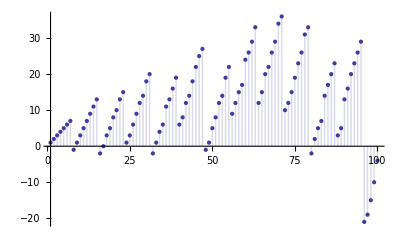

```mathematica
DiscretePlot[tk1b[n,2,8],{n,1,100}]
```

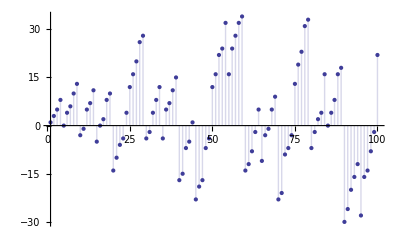

```mathematica
DiscretePlot[tk1[n,2,5],{n,1,100}]
```

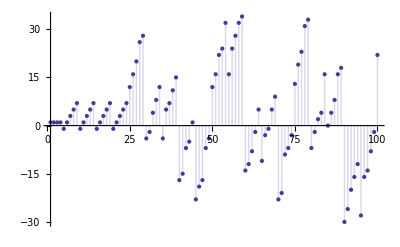

```mathematica
DiscretePlot[tk1z[n,2,5],{n,1,100}]
```

```mathematica
DiscretePlot[tk1[n,aa=3,bb=1.7]-tk1z[n,aa,bb],{n,1,200}]
```

-Graphics-

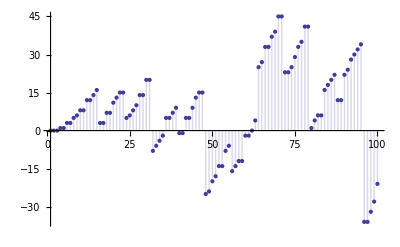

```mathematica
DiscretePlot[tk[n,2,8],{n,1,100}]
```

```mathematica
DiscretePlot[tk2a[n,2,8],{n,1,100}]
```

-Graphics-

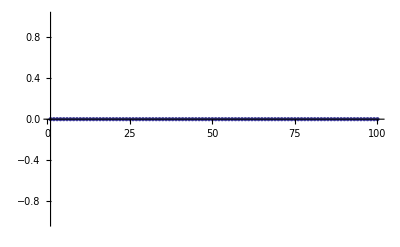

```mathematica
DiscretePlot[tk[n,2,8]-tk2a[n,2,8],{n,1,100}]
```

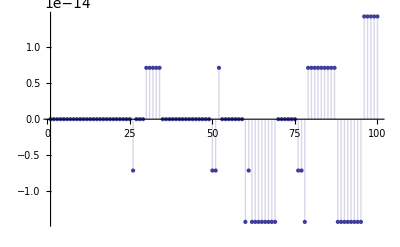

```mathematica
DiscretePlot[tk[n,2,8.71]-tk2a[n,2,8.71],{n,1,100}]
```

```mathematica
Table[{n,ax=tk1[n,aa=3,bb=1.2],bx=tk1z[n,aa,bb],ax-bx},{n,1,100}]//TableForm
```

1 | 1. | 1. | 0.
2 | 2.992 | 2.992 | -8.88178×10^-16
3 | 8.152 | 8.152 | -1.77636×10^-15
4 | -1.832 | -1.832 | -2.22045×10^-15
5 | -7.472 | -7.472 | 0.
6 | 11.464 | 11.464 | 0.
7 | 4.096 | 4.096 | 0.
8 | -5.344 | -5.344 | 2.66454×10^-15
9 | 23.552 | 23.552 | -1.42109×10^-14
10 | -3.448 | -3.448 | -9.76996×10^-15
11 | -24.64 | -24.64 | 1.42109×10^-14
12 | 4.16 | 4.16 | 9.76996×10^-15
13 | 27.896 | 27.896 | -7.10543×10^-15
14 | 8.816 | 8.816 | -1.06581×10^-14
15 | -8.104 | -8.104 | 3.55271×10^-15
16 | -1.312 | -1.312 | -2.04281×10^-14
17 | -30.712 | -30.712 | -3.55271×10^-15
18 | 17.096 | 17.096 | 7.10543×10^-15
19 | 33.056 | 33.056 | 7.10543×10^-15
20 | -8.128 | -8.128 | -1.06581×10^-14
21 | -2.152 | -2.152 | -1.77636×10^-15
22 | -19.072 | -19.072 | 1.77636×10^-14
23 | -32.056 | -32.056 | 1.42109×10^-14
24 | -2.056 | -2.056 | -4.44089×10^-16
25 | 1.352 | 1.352 | 1.77636×10^-15
26 | 40.16 | 40.16 | -6.39488×10^-14
27 | 17.76 | 17.76 | -3.55271×10^-14
28 | 12. | 12. | -3.01981×10^-14
29 | -15.24 | -15.24 | 3.19744×10^-14
30 | -15.024 | -15.024 | 1.06581×10^-14
31 | 26.856 | 26.856 | -3.55271×10^-14
32 | 23.232 | 23.232 | 1.06581×10^-14
33 | -8.952 | -8.952 | -7.10543×10^-15
34 | -51.792 | -51.792 | 7.10543×10^-15
35 | 44.904 | 44.904 | 3.55271×10^-14
36 | 9.624 | 9.624 | 2.13163×10^-14
37 | -2.928 | -2.928 | -1.06581×10^-14
38 | 34.152 | 34.152 | -9.23706×10^-14
39 | -4.8 | -4.8 | 5.32907×10^-15
40 | -12.384 | -12.384 | 9.76996×10^-14
41 | 35.976 | 35.976 | 7.10543×10^-15
42 | -8.304 | -8.304 | -7.81597×10^-14
43 | -5.304 | -5.304 | -7.4607×10^-14
44 | -10.632 | -10.632 | -1.77636×10^-14
45 | -6.024 | -6.024 | 0.
46 | -29.424 | -29.424 | -4.26326×10^-14
47 | 14.616 | 14.616 | 1.24345×10^-14
48 | -9.504 | -9.504 | -9.41469×10^-14
49 | 4.272 | 4.272 | -8.26006×10^-14
50 | 11.472 | 11.472 | -1.47438×10^-13
51 | -43.032 | -43.032 | 6.39488×10^-14
52 | 73.032 | 73.032 | -1.42109×10^-14
53 | 11.232 | 11.232 | -6.21725×10^-14
54 | -15.792 | -15.792 | 3.90799×10^-14
55 | 32.088 | 32.088 | 4.26326×10^-14
56 | -6.6 | -6.6 | 6.75016×10^-14
57 | 30.48 | 30.48 | -6.75016×10^-14
58 | -8.472 | -8.472 | -7.28306×10^-14
59 | -42.624 | -42.624 | 4.26326×10^-14
60 | -40.464 | -40.464 | 1.27898×10^-13
61 | 63.624 | 63.624 | 1.7053×10^-13
62 | 53.184 | 53.184 | 1.20792×10^-13
63 | -55.824 | -55.824 | 2.20268×10^-13
64 | 33.952 | 33.952 | -1.27898×10^-13
65 | 12.712 | 12.712 | 4.61853×10^-14
66 | -8.24 | -8.24 | 9.05942×10^-14
67 | 33.64 | 33.64 | 1.63425×10^-13
68 | -58.952 | -58.952 | 1.13687×10^-13
69 | -82.352 | -82.352 | -4.26326×10^-14
70 | 54.808 | 54.808 | -3.05533×10^-13
71 | 67.744 | 67.744 | 9.9476×10^-14
72 | 11.104 | 11.104 | -1.06581×10^-13
73 | -32.552 | -32.552 | -1.42109×10^-13
74 | 4.528 | 4.528 | -1.34115×10^-13
75 | 62.704 | 62.704 | 1.13687×10^-13
76 | 15.904 | 15.904 | 1.81188×10^-13
77 | -94.04 | -94.04 | -1.27898×10^-13
78 | -0.944 | -0.944 | 1.66089×10^-13
79 | 2.056 | 2.056 | 1.66089×10^-13
80 | -26.816 | -26.816 | 2.13163×10^-14
81 | 106.984 | 106.984 | 1.42109×10^-14
82 | 46. | 46. | 2.84217×10^-14
83 | -22.28 | -22.28 | 1.10134×10^-13
84 | -26.6 | -26.6 | -3.55271×10^-14
85 | -15.008 | -15.008 | 7.10543×10^-15
86 | -16.808 | -16.808 | -2.84217×10^-14
87 | -21.632 | -21.632 | 3.33955×10^-13
88 | 10.528 | 10.528 | 1.04805×10^-13
89 | -34.424 | -34.424 | -2.13163×10^-13
90 | -37.448 | -37.448 | -1.91847×10^-13
91 | 49.312 | 49.312 | -4.83169×10^-13
92 | -2.672 | -2.672 | -3.2685×10^-13
93 | 94.888 | 94.888 | 4.26326×10^-14
94 | -6.272 | -6.272 | 4.9738×10^-14
95 | -8.072 | -8.072 | 3.17968×10^-13
96 | -5.984 | -5.984 | 2.27374×10^-13
97 | -41.864 | -41.864 | -2.84217×10^-14
98 | -0.104 | -0.104 | -3.64153×10^-13
99 | -30.056 | -30.056 | -2.70006×10^-13
100 | 34.024 | 34.024 | -1.84741×10^-13

```mathematica
Table[{n,tk1z[n,.5,1.1]},{n,1,100}]//TableForm
```

1 | 1.
2 | 0.546603
3 | 0.525095
4 | 0.387578
5 | 0.505547
6 | 0.328804
7 | 0.478961
8 | 0.346368
9 | 0.341108
10 | 0.214264
11 | 0.38739
12 | 0.42779
13 | 0.534728
14 | 0.49209
15 | 0.298238
16 | 0.241158
17 | 0.483764
18 | 0.358518
19 | 0.470429
20 | 0.36407
21 | 0.185242
22 | 0.170834
23 | 0.500926
24 | 0.387078
25 | 0.517538
26 | 0.293447
27 | 0.403165
28 | 0.193134
29 | 0.454014
30 | 0.313443
31 | 0.47445
32 | 0.33536
33 | 0.408498
34 | 0.484454
35 | 0.344241
36 | 0.176818
37 | 0.467123
38 | 0.338717
39 | 0.298609
40 | 0.283349
41 | 0.393976
42 | 0.208859
43 | 0.42788
44 | 0.437741
45 | 0.460983
46 | 0.248976
47 | 0.587357
48 | 0.335895
49 | 0.523482
50 | 0.338514
51 | 0.370105
52 | 0.164122
53 | 0.470252
54 | 0.32399
55 | 0.226865
56 | 0.280232
57 | 0.237386
58 | 0.276794
59 | 0.418023
60 | 0.266621
61 | 0.463564
62 | 0.508225
63 | 0.383374
64 | 0.419404
65 | 0.265102
66 | 0.190146
67 | 0.505506
68 | 0.322644
69 | 0.294885
70 | 0.231693
71 | 0.479097
72 | 0.316032
73 | 0.559502
74 | 0.396346
75 | 0.385228
76 | 0.287133
77 | 0.380846
78 | 0.378825
79 | 0.475099
80 | 0.419391
81 | 0.285246
82 | 0.229364
83 | 0.511004
84 | 0.357515
85 | 0.394483
86 | 0.419498
87 | 0.301859
88 | 0.260457
89 | 0.552852
90 | 0.351436
91 | 0.350822
92 | 0.133348
93 | 0.266709
94 | 0.274559
95 | 0.285037
96 | 0.0882377
97 | 0.411169
98 | 0.148082
99 | 0.135323
100 | 0.151354

```mathematica
$RecursionLimit=1000000
```

1000000

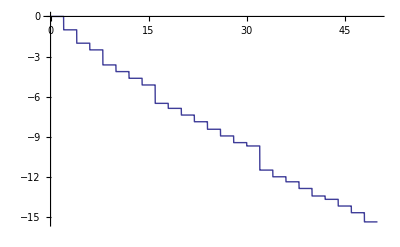

```mathematica
Plot[ tk1z[n,.5,2]-DD[n,.5],{n,0,50}]
```

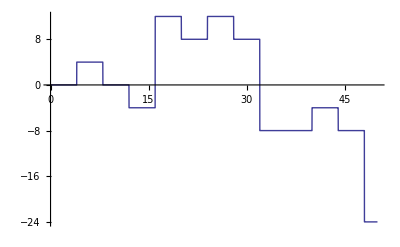

```mathematica
-Plot[ tk1z[n,-1,4]-DD[n,-1],{n,0,50}]
```

```mathematica
Table[ {n,((tk1z[n,aa=-1,4]-DD[n,aa])-((tk1z[n-1,aa,4]-DD[n-1,aa]))),If[Mod[n,4]==0,4 MoebiusMu[Floor[n/4]],0]+If[Mod[n,16]==0,16 MoebiusMu[Floor[n/16]],0]+
If[Mod[n,64]==0,64 MoebiusMu[Floor[n/64]],0]},{n,2,100}]//TableForm
```

2 | 0 | 0
3 | 0 | 0
4 | 4 | 4
5 | 0 | 0
6 | 0 | 0
7 | 0 | 0
8 | -4 | -4
9 | 0 | 0
10 | 0 | 0
11 | 0 | 0
12 | -4 | -4
13 | 0 | 0
14 | 0 | 0
15 | 0 | 0
16 | 16 | 16
17 | 0 | 0
18 | 0 | 0
19 | 0 | 0
20 | -4 | -4
21 | 0 | 0
22 | 0 | 0
23 | 0 | 0
24 | 4 | 4
25 | 0 | 0
26 | 0 | 0
27 | 0 | 0
28 | -4 | -4
29 | 0 | 0
30 | 0 | 0
31 | 0 | 0
32 | -16 | -16
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 0 | 0
38 | 0 | 0
39 | 0 | 0
40 | 4 | 4
41 | 0 | 0
42 | 0 | 0
43 | 0 | 0
44 | -4 | -4
45 | 0 | 0
46 | 0 | 0
47 | 0 | 0
48 | -16 | -16
49 | 0 | 0
50 | 0 | 0
51 | 0 | 0
52 | -4 | -4
53 | 0 | 0
54 | 0 | 0
55 | 0 | 0
56 | 4 | 4
57 | 0 | 0
58 | 0 | 0
59 | 0 | 0
60 | 4 | 4
61 | 0 | 0
62 | 0 | 0
63 | 0 | 0
64 | 64 | 64
65 | 0 | 0
66 | 0 | 0
67 | 0 | 0
68 | -4 | -4
69 | 0 | 0
70 | 0 | 0
71 | 0 | 0
72 | 0 | 0
73 | 0 | 0
74 | 0 | 0
75 | 0 | 0
76 | -4 | -4
77 | 0 | 0
78 | 0 | 0
79 | 0 | 0
80 | -16 | -16
81 | 0 | 0
82 | 0 | 0
83 | 0 | 0
84 | 4 | 4
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 4 | 4
89 | 0 | 0
90 | 0 | 0
91 | 0 | 0
92 | -4 | -4
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 16 | 16
97 | 0 | 0
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

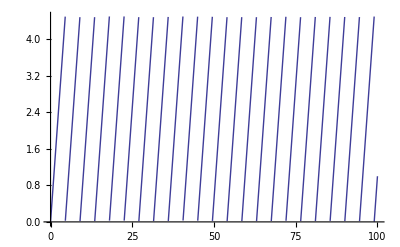

```mathematica
Plot[n-4.5Floor[n/4.5],{n,0,100}]
```